PV Asymmetry

```mathematica
SetDirectory[NotebookDirectory[]];
size=12;
gev2fm=5.067730759;
Gf=1.1663787*10^-5/gev2fm^2;
s2thetaw=0.23868;
alpha=1/137.035999139;
file1="dcs_1p523e08m4+.dat";
file2="dcs_1p523e08m4-.dat";
file3="dcs_1p523e08m4-ns+.dat";
file4="dcs_1p523e08m4-ns-.dat";

commentlength=175;
filelength=Length@Import[file1,"Lines"];
n=filelength-commentlength+3;
xs1=OpenRead[file1];
Skip[xs1,Record,5];
Line6=ReadList[xs1,{Word,Word,Word,Word,Number,Word,Word,Word,Word},1];
Line7=ReadList[xs1,{Word,Word,Word,Word,Word,Number,Word,Word,Word,Number,Word},1];
Skip[xs1,Record,163];
data1=ReadList[xs1,{Number,Number,Number,Number,Number,Number},n];
AW=Line7[[1,10]];
Z=Line7[[1,6]];
m=0.5109989461*10^(-3);
e1=0.155;
M=0.9314940954*AW;
sinv:=M^2+2e1*M;
ecm=(sinv-M^2)/(2Sqrt[sinv]);
qsq[θcm_]:=1/(2sinv)(sinv-M^2)^2(1-Cos[θcm]);
θlab[θcm_]:=2ArcSin[1/Sqrt[4 e1^2/qsq[θcm]-2 e1/M]];
Nneutr=(IntegerPart[AW]-Z);
Qw=Z (1-4*s2thetaw)-Nneutr;
e2[angl_]:=e1/(1+2e1/M*Sin[angl/2]^2);
q[angl_]:=Sqrt[4e1 e2[angl] Sin[angl/2]^2]*gev2fm;
xs2=OpenRead[file2];
Skip[xs2,Record,commentlength-5];
data2=ReadList[xs2,{Number,Number,Number,Number,Number,Number},n];
xs3=OpenRead[file3];
Skip[xs3,Record,commentlength-5];
data3=ReadList[xs3,{Number,Number,Number,Number,Number,Number},n];
xs4=OpenRead[file4];
Skip[xs4,Record,commentlength-5];
data4=ReadList[xs4,{Number,Number,Number,Number,Number,Number},n];

planewavelistq={};planewavelistdeg={};
asymmetrylistdeg1={};asymmetrylistdeg2={};asymmetrylistdeg3={};
asymmetrylistq1={};asymmetrylistq2={};asymmetrylistq3={};
Do[
Aplane=(Gf*q[data1[[i,1]]/180*Pi]^2/(4 Pi alpha 2^(1/2)))(-Qw)/Z;
AppendTo[planewavelistdeg,{data1[[i,2]],Aplane*10^6}];
AppendTo[asymmetrylistdeg1,{data1[[i,2]],(data1[[i,4]]-data2[[i,4]])/(data1[[i,4]]+data2[[i,4]])*10^6}];
AppendTo[asymmetrylistdeg2,{data3[[i,2]],(data3[[i,4]]-data4[[i,4]])/(data3[[i,4]]+data4[[i,4]])*10^6}],{i,1,n}]
```

```mathematica
planewavelistdeg2545={};
asymmetrylistdeg2545={};
asymmetrylistdeglam02545={};
Do[
Aplane=(Gf*q[data1[[i,1]]/180*Pi]^2/(4 Pi alpha 2^(1/2)))(-Qw)/Z;
AppendTo[planewavelistdeg2545,{data1[[i,2]],Aplane*10^6}];
AppendTo[asymmetrylistdeg2545,{data3[[i,2]],(data1[[i,4]]-data2[[i,4]])/(data1[[i,4]]+data2[[i,4]])*10^6}];
AppendTo[asymmetrylistdeglam02545,{data3[[i,2]],(data3[[i,4]]-data4[[i,4]])/(data3[[i,4]]+data4[[i,4]])*10^6}],{i,158,162}]
```

```mathematica
sizemajor:=0.012;
sizeminor:=0.006;
BotTickMajor=Range[0,180,30];
BotTickMinor=Transpose[{Range[0,180,10],""&/@Range[0,180,10],{sizeminor,0}&/@Range[0,180,10]}];
TopTickMajor=Transpose[{Range[0,180,30],NumberForm[q[#/180 Pi],{3,3}]&/@Range[0,180,30]}];
TopTickMajor={{0,0},{30,"0.406"},{60,"0.783"},{90,"1.100"},{120,"1.350"},{150,"1.500"},{180,"1.550"}};
TopTickMinor=Transpose[{Range[0,180,10],""&/@Range[0,180,10]}];
TopTick=TopTickMajor~Join~TopTickMinor;
BotTick=BotTickMajor~Join~BotTickMinor;
```

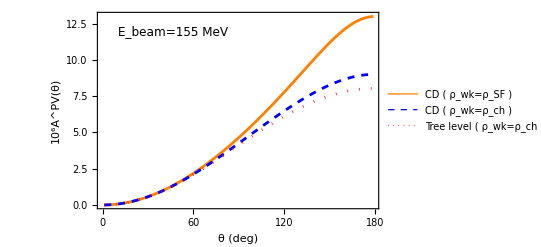

```mathematica
th=0.01;
A1=ListPlot[{asymmetrylistdeg1,asymmetrylistdeg2,planewavelistdeg},Frame->True,PlotRange->All,FrameLabel->{Text[Style["θ (deg)",FontSize->15]],Text[Style["10^6A^PV(θ)",FontSize->15]],Text[Style["q (fm^-1)",FontSize->15]]},PlotStyle->{{Thickness[th/2],Orange},{Thickness[th/2],Dashed,Blue},{Thickness[th/2],Dashing[{0,0.02}],Red}},PlotLegends->Placed[LineLegend[{Text[Style["CD ( ρ_wk=ρ_SF )",FontSize->12]],Text[Style["CD ( ρ_wk=ρ_ch )",FontSize->12]],Text[Style["Tree level ( ρ_wk=ρ_ch )",FontSize->12]]}],{0.31,0.65}],Epilog->{Text[Style["E_beam="<>ToString[Round[e1*1000]]<>" MeV",Black,FontSize->12],Scaled[{.27,.9}]]},Joined->True,FrameTicks->{{All,Automatic},{BotTick,TopTickMajor}},FrameTicksStyle->Directive[FontSize->11]]
```

```mathematica
Export["AsymmetryC12deg.pdf",A1]
```

AsymmetryC12deg.pdf